```mathematica
TI - GibbsBogoliubov -mean value theorem;
```

```mathematica
(*To a fairly good approximation, there exists a dU/dL value at some single lambda value that is equal to Fah. Further and interestingly, the lambda value is the same for all temperatures. Therefore this gives a shortcut to calculate Fah surfaces. 
Eg the method would be something like:
1)  calculate dUdL vs lambda at some temperature, say 3200K.
2) Integrate dUdL for 3200K, and find out what value of lambda sets dUdL equal to integrated dUdL.
3) For other temperatures, rather than doing TILD at lambda-0.0, 0.1 ,0.2 ...1.0, it is only necessary to do the TILD for the lambda value that we previously solved for in step 2. 
This seems quite surprising, that anharmonicity as a function of temperature can be compressed into a single parameter, the lambda value that solves the Fah in a  mean value theorem type approximation *)
```

```mathematica
Import ab intio data;
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];
(*The file T_dudl_meam_4801 contains TILD data - temp and dUdL, for 11 lambda values 0.0 to 1.0 in 0.1 steps. The data is for ZrC 4.801Angstrom*)
filesEinsteinPot={"T_dudl_meam_4685","T_dudl_meam_4801"};
TdUdL4801=ReadList[filesEinsteinPot[[2]],{Number, Number}];
TdUdL4685=ReadList[filesEinsteinPot[[1]],{Number, Number}];
temps={300,760,1900,2500,3200,3805};
lambda=Table[i/10,{i,0,10}]//N;
```

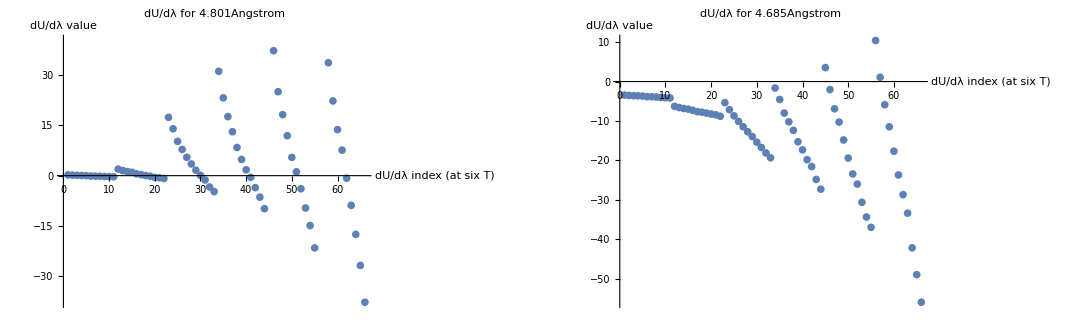

```mathematica
Plot dU/dL data;
(*dUdL given at 6 temperatures - for each of which there are 11 dUdL points - 0.0, 0.1 0.2 .... 1.0 *)
dudlplot1=ListPlot[Transpose[TdUdL4801][[2]],PlotLabel->"dU/dλ for 4.801Angstrom",AxesLabel->{"dU/dλ index \n(at six T)","dU/dλ value"},ImageSize->500];
dudlplot2=ListPlot[Transpose[TdUdL4685][[2]],PlotLabel->"dU/dλ for 4.685Angstrom",AxesLabel->{"dU/dλ index \n(at six T)","dU/dλ value"},ImageSize->500];
GraphicsGrid[{{dudlplot1,dudlplot2}}]
```

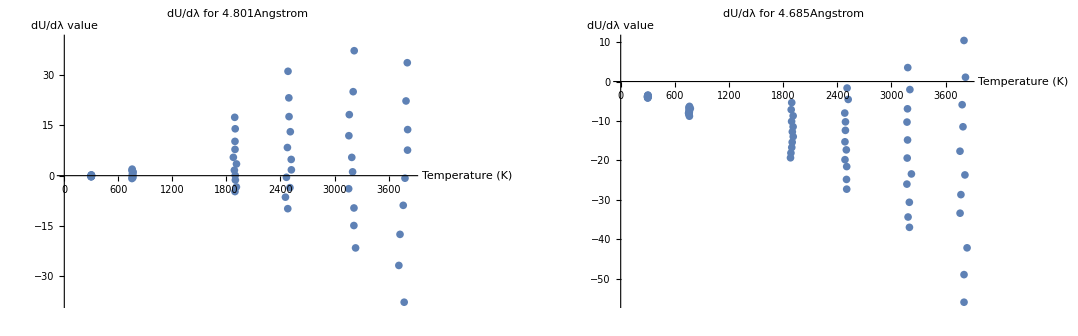

```mathematica
Plot dU/dL data at temperatures;dudlTplotinfo1={PlotLabel->"dU/dλ for 4.801Angstrom",AxesLabel->{"Temperature (K)","dU/dλ value"},ImageSize->500};
dudlT1plot=ListPlot[TdUdL4801,dudlTplotinfo1];
dudlTplotinfo2={PlotLabel->"dU/dλ for 4.685Angstrom",AxesLabel->{"Temperature (K)","dU/dλ value"},ImageSize->500};
dudlT2plot=ListPlot[TdUdL4685,dudlTplotinfo2];
GraphicsGrid[{{dudlT1plot,dudlT2plot}}]
```

```mathematica
Fit polynomial;
(*make the dUdL at function of lambda*)
dUdL4801=Partition[Transpose[TdUdL4801][[2]],11];
dudlLambda4801=Table[Transpose@{lambda,dUdL4801[[i]]},{i,1,6}];
dUdL4685=Partition[Transpose[TdUdL4685][[2]],11];
dudlLambda4685=Table[Transpose@{lambda,dUdL4685[[i]]},{i,1,6}];
(*Fit polynomal function of dudl (in lambda) *)
dudlLambdaFits4801=Table[Fit[dudlLambda4801[[i]],{1,x,x^2,x^3,x^4},x],{i,1,6}];
dudlLambdaFits4685=Table[Fit[dudlLambda4685[[i]],{1,x,x^2,x^3,x^4},x],{i,1,6}];
```

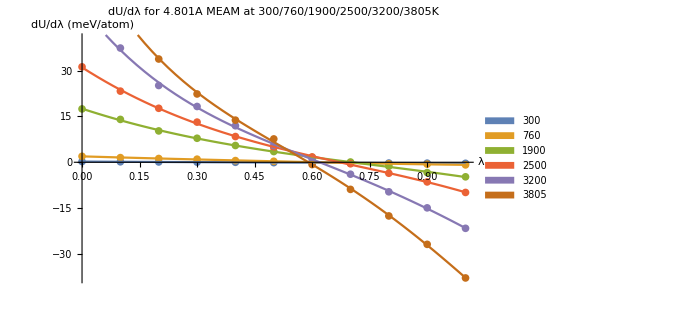

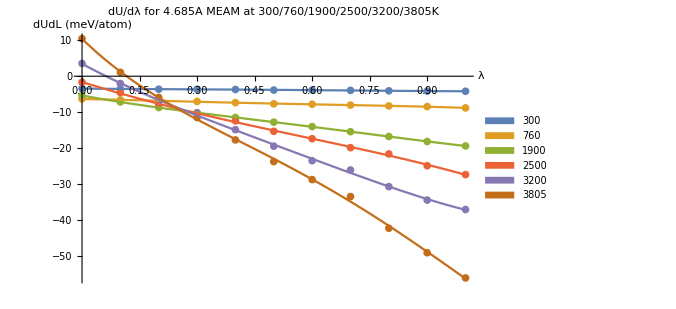

```mathematica
Plot polynomial and data;
(*Plot the dUdL data as a function of lambda, along witht fits, for both 4.685 and 4.801Angstrom*)
(*4801Angstrom*)
dudlLambdaplotinfo4801={PlotLabel->"dU/dλ for 4.801A MEAM at 300/760/1900/2500/3200/3805K",ImageSize->500,AxesLabel->{"λ","dU/dλ \n(meV/atom)"}};
dudlplot4801=Plot[Evaluate@dudlLambdaFits4801,{x,0,1},PlotLegends->SwatchLegend[temps]];
dudldataplot4801=ListPlot[dudlLambda4801,dudlLambdaplotinfo4801];
plot4801=Show[dudldataplot4801,dudlplot4801]
(*4685Angstrom*)
dudlLambdaplotinfo4685={PlotLabel->"dU/dλ for 4.685A MEAM at 300/760/1900/2500/3200/3805K",ImageSize->500,AxesLabel->{"λ","dUdL \n(meV/atom)"}};
dudlplot4685=Plot[Evaluate@dudlLambdaFits4685,{x,0,1},PlotLegends->SwatchLegend[temps]];
dudldataplot4685=ListPlot[dudlLambda4685,dudlLambdaplotinfo4685];
plot4685=Show[dudldataplot4685,dudlplot4685]
(*It is quite interesting - it looks like the temperature dependence of the dUdL is rotation about some single point. If point is at 0.5, the integral is roughly zero, about 0.5 Fah is positive and below it is negative, roughly.*)
```

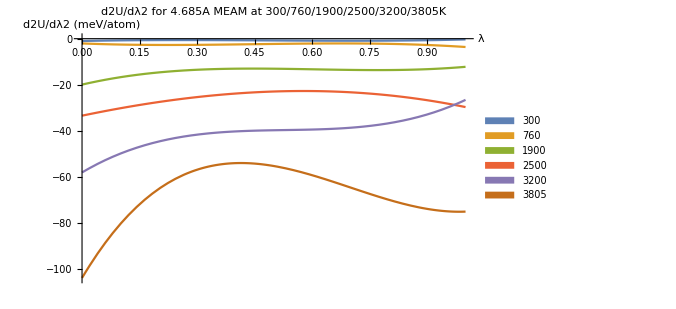

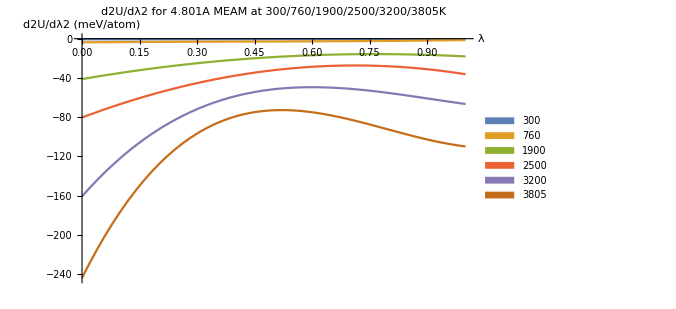

```mathematica
Plot second derivative in lambda;
(*Plot gradients 4.685angstrom*)
DdudlLambda4685=D[dudlLambdaFits4685,x];
DdudlLambdaplotinfo4685={PlotLabel->"d2U/dλ2 for 4.685A MEAM at 300/760/1900/2500/3200/3805K",ImageSize->500,AxesLabel->{"λ","d2U/dλ2 \n(meV/atom)"}};
Plot[Evaluate@Table[DdudlLambda4685[[j]],{j,1,6}],{x,0,1},Evaluate@DdudlLambdaplotinfo4685,PlotLegends->SwatchLegend[temps]]
(*Plot gradients 4.685angstrom*)
DdudlLambda4801=D[dudlLambdaFits4801,x];
DdudlLambdaplotinfo4801={PlotLabel->"d2U/dλ2 for 4.801A MEAM at 300/760/1900/2500/3200/3805K",ImageSize->500,AxesLabel->{"λ","d2U/dλ2 \n(meV/atom)"}};
Plot[Evaluate@Table[DdudlLambda4801[[j]],{j,1,6}],{x,0,1},Evaluate@DdudlLambdaplotinfo4801,PlotLegends->SwatchLegend[temps]]
(*According to Gibbs-Bogoliubov, the second derivative of the Fah should be strictly less than zero, because the second derivative is the variance of the anharmonic perturbation. This is shown to be true. But the third derivative is not constant or always negative or positive. It might be possible to make the third derivative zero though, by fitting a potential where the optimisation function is minimising the anharmonic perturbation variance.*)
```

```mathematica
(*Plot data for second derivative with limits as linear extrapolations of the gradients at the lambda extrema*)
```

```mathematica
limit04801=(dudlLambdaFits4801/.x->0)+(DdudlLambda4801/.x->0)x;
limit14801=(dudlLambdaFits4801/.x->1)-(DdudlLambda4801/.x->1)+(DdudlLambda4801/.x->1)x;
dataplot4801=Table[{limit04801[[i]],limit14801[[i]],dudlLambdaFits4801[[i]]},{i,1,6}];

limit04685=(dudlLambdaFits4685/.x->0)+(DdudlLambda4685/.x->0)x;
limit14685=(dudlLambdaFits4685/.x->1)-(DdudlLambda4685/.x->1)+(DdudlLambda4685/.x->1)x;
dataplot4685=Table[{limit04685[[i]],limit14685[[i]],dudlLambdaFits4685[[i]]},{i,1,6}];

swatchlabels={"λ=0 limit","λ=1 limit", "dU/dλ"};
ps1:={PlotLabel->temps[[i]]"K and 4.685Ang",AxesLabel->{"","dU/dλ \n (meV/atom)"},PlotLegends->Placed[SwatchLegend[swatchlabels],{0.5,0.9}],ImageSize->800}
ps2:={PlotLabel->temps[[i]]"K and 4.801Ang",AxesLabel->{"","dU/dλ \n (meV/atom)"},PlotLegends->Placed[SwatchLegend[swatchlabels],{0.5,0.9}],ImageSize->800}
```

```mathematica
Plot dUdL with limits based on second derivatives at lambda zero and one;
```

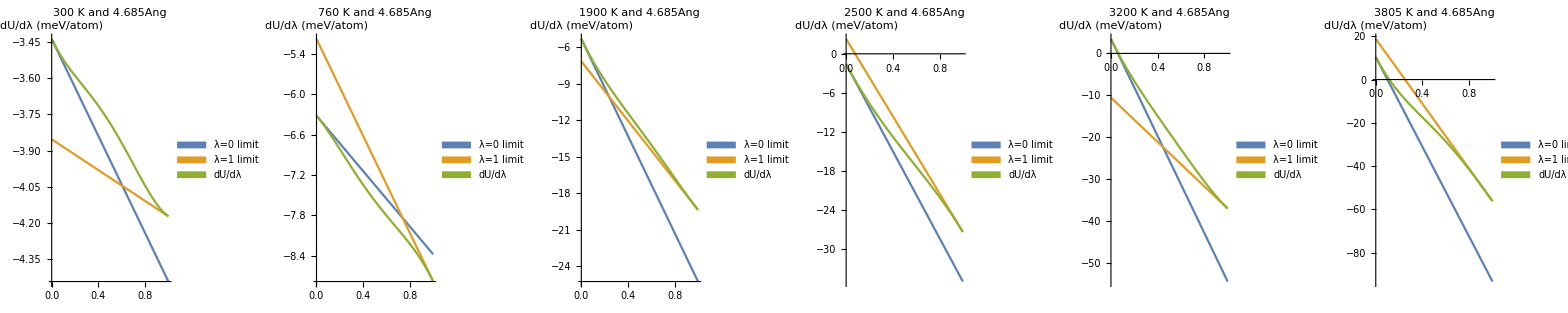
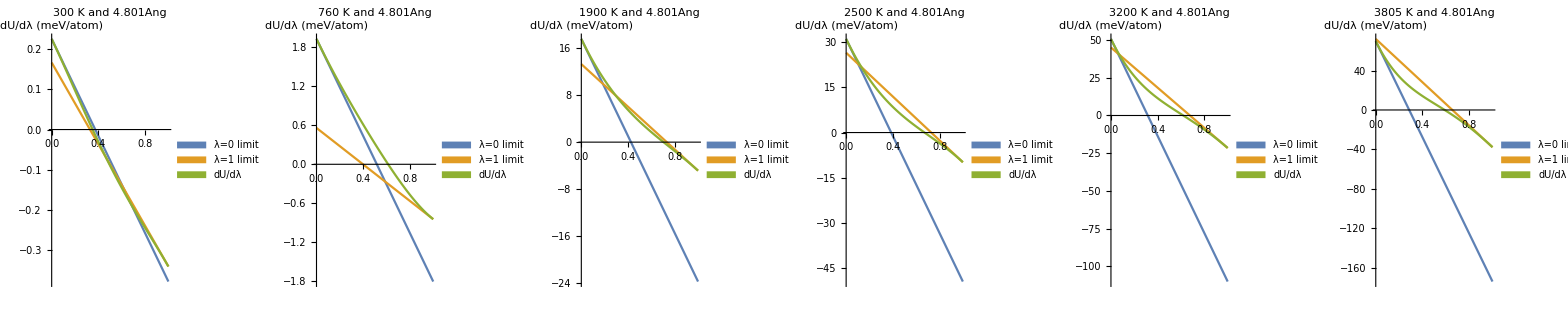

```mathematica
GraphicsGrid[{Table[Plot[Evaluate@dataplot4685[[i]],{x,0,1},Evaluate@(ps1)],{i,1,6}]},ImageSize->2500]GraphicsGrid[{Table[Plot[Evaluate@dataplot4801[[i]],{x,0,1},Evaluate@(ps2)],{i,1,6}]},ImageSize->2500]
```

#### Integrate dudl to find Fah;

```mathematica
(*Test approximate methods to get Fah*)

"Exact integrated dU/dL values (6 temperatures x 2 volumes):"
intVals=Integrate[{dudlLambdaFits4685,dudlLambdaFits4801},{x,0,1}];
intVals//TableForm

"Average of dUdL at lambda=0 lambda=1.0"
diffhalfVals=0.5(({dudlLambdaFits4685,dudlLambdaFits4801}/.x->1)+({dudlLambdaFits4685,dudlLambdaFits4801}/.x->0));
diffhalfVals//TableForm

"dUdL at lambda=0.5"
halfVals={dudlLambdaFits4685,dudlLambdaFits4801}/.x->0.5;
halfVals//TableForm

"Mean value theorem"
meanVals={dudlLambdaFits4685/.x->0.45,dudlLambdaFits4801/.x->0.49};
meanVals//TableForm
```

Exact integrated dU/dL values (6 temperatures x 2 volumes):

-3.80704 | -7.54544 | -12.6831 | -14.8545 | -18.4902 | -23.388
-0.076319 | 0.38386 | 4.42656 | 6.88962 | 8.43487 | 8.78051

Average of dUdL at lambda=0 lambda=1.0

-3.80524 | -7.55287 | -12.3528 | -14.4858 | -16.8191 | -22.8981
-0.0576224 | 0.542028 | 6.34182 | 10.596 | 14.5982 | 16.0412

dUdL at lambda=0.5

-3.78718 | -7.58725 | -12.731 | -15.0607 | -18.9689 | -22.9179
-0.0896737 | 0.318252 | 3.47294 | 5.0255 | 5.98513 | 6.61869

Mean value theorem

-3.74984 | -7.47048 | -12.0816 | -13.9075 | -16.98 | -20.1876
-0.0839421 | 0.34708 | 3.66145 | 5.34893 | 6.50295 | 7.3496

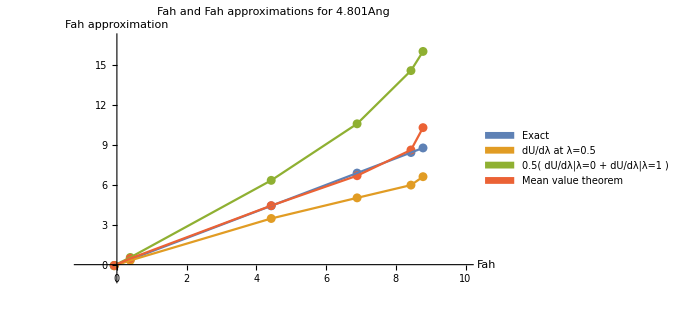

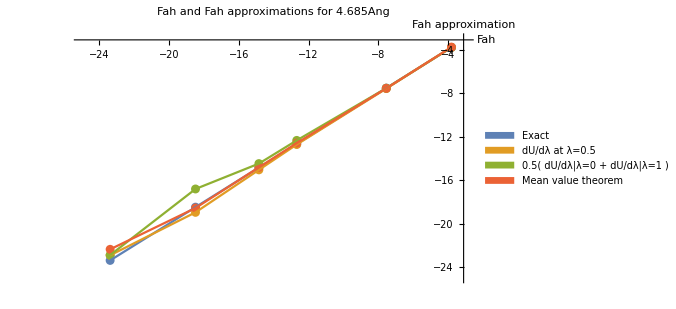

```mathematica
(*Plot different Fah approximations*)
meanVals={dudlLambdaFits4685/.x->0.49,dudlLambdaFits4801/.x->0.45};
plotinfos={{PlotLabel->"Fah and Fah approximations for 4.685Ang",AxesLabel->{"Fah","Fah \n approximation"},ImageSize->500,PlotRange->{{-25,-3},{-25,-3}}},{PlotLabel->"Fah and Fah approximations for 4.801Ang",AxesLabel->{"Fah","Fah \n approximation"},ImageSize->500,PlotRange->{{-1,10},{-1,17}}}};
plots=Table[ListPlot[{Table[Transpose[{intVals[[i]],intVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],halfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],diffhalfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],meanVals[[i]]}],{i,1,2}][[j]]},plotinfos[[j]],PlotLegends->SwatchLegend[{"Exact","dU/dλ at λ=0.5","0.5( dU/dλ|λ=0 + dU/dλ|λ=1 )","Mean value theorem"}]],{j,1,2}];
plotsJoined=Table[ListPlot[{Table[Transpose[{intVals[[i]],intVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],halfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],diffhalfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],meanVals[[i]]}],{i,1,2}][[j]]},plotinfos[[j]],Joined->True],{j,1,2}];
Show[plots[[2]],plotsJoined[[2]]]
Show[plots[[1]],plotsJoined[[1]]]
```

```mathematica
Show Fah approximations making mean value theorem approximation a manipulate variable;
(*Mean value theorem says for an analytic function, eg Fah, its average value can be given by the derivative at some point. There exists some lambda for which dUdL is equal to the integrated dUdL ie Fah.  By making the lambda value at which to take the derivative in the mean value theorem a variable, we can see if there is a single lambda value which can give all Fah. If this is possible, this would be interesting, as we are compressing anharmonicity into a single couple parameter value.*)

(*4.685Angstrom*)
Manipulate[Show[Table[ListPlot[{Table[Transpose[{intVals[[i]],intVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],halfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],diffhalfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],{dudlLambdaFits4685/.x->u
,dudlLambdaFits4801/.x->u}[[i]]}],{i,1,2}][[j]]},plotinfos[[j]],PlotLegends->SwatchLegend[{"Exact","dU/dλ at λ=0.5","0.5( dU/dλ|λ=0 + dU/dλ|λ=1 )","Mean value theorem"}]],{j,1,2}][[1]],Table[ListPlot[{Table[Transpose[{intVals[[i]],intVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],halfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],diffhalfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],{dudlLambdaFits4685/.x->u
,dudlLambdaFits4801/.x->u}[[i]]}],{i,1,2}][[j]]},plotinfos[[j]],Joined->True],{j,1,2}][[1]]],{{u,0.25,"λ for mean-value theorem"},0,1}]

(*4.801Angstrom*)
Manipulate[Show[Table[ListPlot[{Table[Transpose[{intVals[[i]],intVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],halfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],diffhalfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],{dudlLambdaFits4685/.x->u
,dudlLambdaFits4801/.x->u}[[i]]}],{i,1,2}][[j]]},plotinfos[[j]],PlotLegends->SwatchLegend[{"Exact","dU/dλ at λ=0.5","0.5( dU/dλ|λ=0 + dU/dλ|λ=1 )","Mean value theorem"}]],{j,1,2}][[2]],Table[ListPlot[{Table[Transpose[{intVals[[i]],intVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],halfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],diffhalfVals[[i]]}],{i,1,2}][[j]],Table[Transpose[{intVals[[i]],{dudlLambdaFits4685/.x->u
,dudlLambdaFits4801/.x->u}[[i]]}],{i,1,2}][[j]]},plotinfos[[j]],Joined->True],{j,1,2}][[2]]],{{u,0.25,"λ for mean-value theorem"},0,1}]
```

```mathematica
(*For 4.685Ang the lambda value of 0.496 works well across all temperatures*)
(*For 4.801Ang the lambda value of 0.458 works well across all temperatures*)
```